```mathematica
Manipulate[Graphics[Line[{{0,0},p}],PlotRange->2],{{p,{1,1}},Locator}]
```

```mathematica
Deploy[Graphics[{Cyan,Disk[],Locator[{0,0}]},PlotRange->1]]
```

-Graphics-

```mathematica
DynamicModule[{pt={0,0}},ClickPane[Dynamic@Graphics[{Yellow,Disk[],Black,Point[pt]},ImageSize->Tiny],(pt=#)&]]
```

```mathematica
DynamicModule[{pt={0,0}},ClickPane[Framed@Graphics[{Yellow,Dynamic@Disk[pt]},PlotRange->5],(pt=#)&]]
```



```mathematica
{Annotation[Graphics[Disk[]],"An annotation","Mouse"],Dynamic[MouseAnnotation[]]}
```

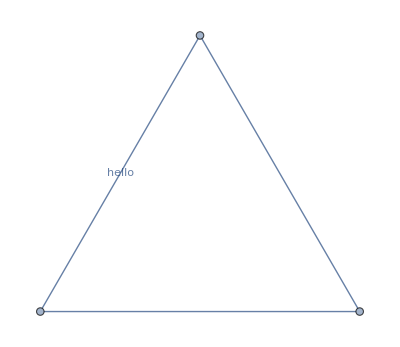

```mathematica
Graph[{Annotation[1<->2,EdgeLabels->"hello"],2<->3,3<->1}]
```

```mathematica
(*If the mouse is over the graphics,MouseAnnotation will return the associated annotation:*)
Annotation[Graphics[Disk[]],"An annotation","Mouse"]
(* When the mouse is over the graphics,the annotation is displayed *)Dynamic[MouseAnnotation[]]
```

-Graphics-